```mathematica
Print[Button[Style["Quit Kernel",Bold],Quit[],ImageSize->{150,35}]]
```

Quit Kernel

Das folgende Programm gilt für homogene Differentialgleichungssysteme in der Form:

ⅆ/ⅆt 𝓎(t)=𝒜·𝓎(t)

Die Lösung eines allgemeinen Differentialgleichungssystems erhält man wie folgt:

𝓎(t)=ⅇ^(t·𝒜)·(𝓋_0+∫_0^t ⅇ^(-τ·𝒜)·𝓈(τ)ⅆτ)=ⅇ^(t·𝒜)·𝓋_0+∫_0^t ⅇ^((t-τ)·𝒜)·𝓈(τ)ⅆτ=Re[ⅇ^(t·𝒜)]·𝓋_0+∫_0^t Re[ⅇ^((t-τ)·𝒜)]·𝓈(τ)ⅆτ

Durch Diagonalisierung (Auflistung der Eigenvektoren in der Matrix 𝒫 und den Eigenwerten λ auf der Hauptdiagonalen der Diagonalmatrix 𝒟) des Matrixexponentials folgt:

𝓎(t)=Re[𝒫·𝒟[ⅇ^(λ·t)]·𝒫^-1]·𝓋_0+∫_0^t Re[𝒫·𝒟[ⅇ^(λ·(t-τ))]·𝒫^-1]·𝓈[τ]ⅆτ

Für den homogenen Fall folgt:

𝓎(t)=Re[𝒫·𝒟[ⅇ^(λ·t)]·𝒫^-1]·𝓋_0=Re[𝒫·𝒟[ⅇ^(λ·t)]·𝒫^-1·𝓋_0]=Re[𝒫·𝒟[ⅇ^(λ·t)]·𝒸]=Re[∑_(i=1)^n c_i 𝓅_i ⅇ^(λ_i t)]

Hinweis zum Programm: Realteilbildung von 𝓎(t) optional bereits in der allgemeinen Lösung möglich (ComplexExpand[Re[…]] um die Summe)

## Eingabe (𝒜)

```mathematica
ClearAll["Global`*"]
𝒜=({{0, 0, 1, 0}, {0, 0, 0, 1}, {-30, 10, -1.5, 0}, {10, -5, 0, -.5}})//N;
```

## Eingabe (𝒩ℯ𝒷ℯ𝓃𝒷ℯ𝒹𝒾𝓃ℊ𝓊𝓃ℊℯ𝓃)

Die Nebenbedingungen des Differentialgleichungssystems werden wie folgt defniniert:

```mathematica
𝒩ℯ𝒷ℯ𝓃𝒷ℯ𝒹𝒾𝓃ℊ𝓊𝓃ℊℯ𝓃=({{Funktion, Zeit, Wert}});
```

```mathematica
𝒩ℯ𝒷ℯ𝓃𝒷ℯ𝒹𝒾𝓃ℊ𝓊𝓃ℊℯ𝓃=({{1, 0, 0}, {1, 1, .01}, {1, 2, .02}, {1, 3, .008}, {1, 4, .005}})//N;
```

```mathematica
(*Ausgabe*)
Print[StringForm["Nebenbedingungen:\n``\n→ Es handelt sich um ein `` Differentialgleichungssystem.",
TableForm[Table[
{Subscript[y, Rationalize[𝒩ℯ𝒷ℯ𝓃𝒷ℯ𝒹𝒾𝓃ℊ𝓊𝓃ℊℯ𝓃[[i,1]]]],𝒩ℯ𝒷ℯ𝓃𝒷ℯ𝒹𝒾𝓃ℊ𝓊𝓃ℊℯ𝓃[[i,2]],𝒩ℯ𝒷ℯ𝓃𝒷ℯ𝒹𝒾𝓃ℊ𝓊𝓃ℊℯ𝓃[[i,3]]},
{i,Length[𝒩ℯ𝒷ℯ𝓃𝒷ℯ𝒹𝒾𝓃ℊ𝓊𝓃ℊℯ𝓃]}],TableHeadings->{None,{"Funktion","Zeit","Wert"}}],
Which[
Length[𝒜]==Length[𝒩ℯ𝒷ℯ𝓃𝒷ℯ𝒹𝒾𝓃ℊ𝓊𝓃ℊℯ𝓃],"bestimmtes",
Length[𝒜]<Length[𝒩ℯ𝒷ℯ𝓃𝒷ℯ𝒹𝒾𝓃ℊ𝓊𝓃ℊℯ𝓃],"überbestimmtes",
Length[𝒜]>Length[𝒩ℯ𝒷ℯ𝓃𝒷ℯ𝒹𝒾𝓃ℊ𝓊𝓃ℊℯ𝓃],"unterbestimmtes"]]]
```

Nebenbedingungen:
Funktion | Zeit | Wert
y_1 | 0. | 0.
y_1 | 1. | 0.01
y_1 | 2. | 0.02
y_1 | 3. | 0.008
y_1 | 4. | 0.005
→ Es handelt sich um ein überbestimmtes Differentialgleichungssystem.

## Programm (allgemein)

```mathematica
(*Programm*)
λ=Chop[Eigenvalues[𝒜]];
𝒫=Chop[Transpose[Eigenvectors[𝒜]]];
𝓎𝒜ℓℓℊℯ𝓂ℯ𝒾𝓃[t_]=Sum[Subscript[c, i] 𝒫[[All,i]]Exp[λ[[i]]t],{i,Length[𝒜]}];

(*Ausgabe*)
Print[StringForm["λ = ``\n𝒫 = ``\n𝓎_allgemein(t) = ``",
λ//MatrixForm,
𝒫//MatrixForm,
𝓎𝒜ℓℓℊℯ𝓂ℯ𝒾𝓃[t]//MatrixForm]]
```

λ = (-0.694329+5.73778 ⅈ
-0.694329-5.73778 ⅈ
-0.305671+1.18464 ⅈ
-0.305671-1.18464 ⅈ)
𝒫 = (-0.0193075-0.159553 ⅈ | -0.0193075+0.159553 ⅈ | -0.0603432-0.202367 ⅈ | -0.0603432+0.202367 ⅈ
0.0169152+0.0543156 ⅈ | 0.0169152-0.0543156 ⅈ | -0.149054-0.577667 ⅈ | -0.149054+0.577667 ⅈ
0.928885 | 0.928885 | 0.258178-0.00962737 ⅈ | 0.258178+0.00962737 ⅈ
-0.323396+0.0593427 ⅈ | -0.323396-0.0593427 ⅈ | 0.729891 | 0.729891)
𝓎_allgemein(t) = …

## Programm (überbestimmt)

```mathematica
(*Programm*)
ℊℓℯ𝒾𝒸𝒽𝓊𝓃ℊℯ𝓃=Table[
𝓎𝒜ℓℓℊℯ𝓂ℯ𝒾𝓃[𝒩ℯ𝒷ℯ𝓃𝒷ℯ𝒹𝒾𝓃ℊ𝓊𝓃ℊℯ𝓃[[i,2]]][[𝒩ℯ𝒷ℯ𝓃𝒷ℯ𝒹𝒾𝓃ℊ𝓊𝓃ℊℯ𝓃[[i,1]]]]==𝒩ℯ𝒷ℯ𝓃𝒷ℯ𝒹𝒾𝓃ℊ𝓊𝓃ℊℯ𝓃[[i,3]],
{i,Length[𝒩ℯ𝒷ℯ𝓃𝒷ℯ𝒹𝒾𝓃ℊ𝓊𝓃ℊℯ𝓃]}];
𝒜𝒢ℓℯ𝒾𝒸𝒽𝓊𝓃ℊℯ𝓃=Normal[CoefficientArrays[ℊℓℯ𝒾𝒸𝒽𝓊𝓃ℊℯ𝓃,Table[Subscript[c, i],{i,Length[𝒜]}]]][[2]];
𝒷𝒢ℓℯ𝒾𝒸𝒽𝓊𝓃ℊℯ𝓃=-Transpose[{Normal[CoefficientArrays[ℊℓℯ𝒾𝒸𝒽𝓊𝓃ℊℯ𝓃,Table[Subscript[c, i],{i,Length[𝒜]}]]][[1]]}];
𝒸=Flatten[LeastSquares[𝒜𝒢ℓℯ𝒾𝒸𝒽𝓊𝓃ℊℯ𝓃,𝒷𝒢ℓℯ𝒾𝒸𝒽𝓊𝓃ℊℯ𝓃]];

𝓇ℯℊℯℓ𝓃={(a_ Cos[c_]+b_ Sin[c_]):>√(a^2+b^2) Cos[c-Arg[a+I b]],
(Cos[c_]+b_ Sin[c_]):>√(1+b^2)Cos[c-Arg[1+I b]],
(a_ Cos[c_]+Sin[c_]):>√(a^2+1)Cos[c-Arg[a+I ]],
(Cos[c_]+Sin[c_]):>√2 Cos[c-π/4],
1.t:>t,-1.t:>-t,ⅇ^(1.t):>ⅇ^t,ⅇ^(-1.t):>ⅇ^-t};
𝓎[t_]=FullSimplify[Chop[ComplexExpand[Re[𝓎𝒜ℓℓℊℯ𝓂ℯ𝒾𝓃[t]/.Table[Subscript[c, i]->𝒸[[i]],{i,Length[𝒸]}]]]]]/.𝓇ℯℊℯℓ𝓃;

(*Ausgabe*)
Print[StringForm["𝒸 = ``\n𝓎(t) = ``",
𝒸//MatrixForm,
𝓎[t]//MatrixForm]]
```

𝒸 = (-0.140353+0.032835 ⅈ
-0.140353-0.032835 ⅈ
0.00442908-0.0388353 ⅈ
0.00442908+0.0388353 ⅈ)
𝓎(t) = (0.0165082 ⅇ^(-0.305671 t) Cos[2.96536+1.18464 t]+0.0463323 ⅇ^(-0.694329 t) Cos[1.22056+5.73778 t]
0.0164001 ⅇ^(-0.694329 t) Cos[2.10251-5.73778 t]+0.0466377 ⅇ^(-0.305671 t) Cos[3.00263+1.18464 t]
0.0201969 ⅇ^(-0.305671 t) Cos[1.49451-1.18464 t]+0.267784 ⅇ^(-0.694329 t) Cos[2.91178+5.73778 t]
0.0947869 ⅇ^(-0.694329 t) Cos[0.411292-5.73778 t]+0.0570586 ⅇ^(-0.305671 t) Cos[1.45724-1.18464 t])

## Plot

Unterbestimmter Fall: Bei dem Plot von 𝓎(t) müssen den übrigen Parametern c_i konstante Werte zugeordnet werden:

```mathematica
𝓉ℬℯ𝓇ℯ𝒾𝒸𝒽={0,10};
𝒸𝒫ℓℴ𝓉={};
```

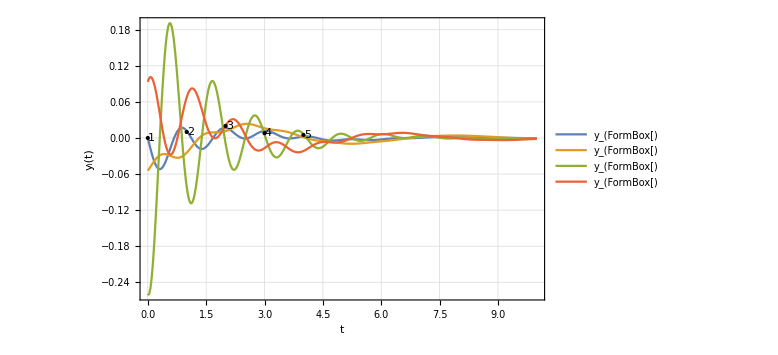

```mathematica
(*Ausgabe*)
plot=Plot[
Evaluate[𝓎[t]/.𝒸𝒫ℓℴ𝓉],{t,𝓉ℬℯ𝓇ℯ𝒾𝒸𝒽[[1]],𝓉ℬℯ𝓇ℯ𝒾𝒸𝒽[[2]]},
PlotRange->All,Frame->True,FrameLabel->{"t","y_i(t)"},GridLines->Automatic,
PlotLegends->Table[StringForm["y_(``)",i],{i,Length[𝓎[t]]}],
Epilog->
{Table[
Point[{𝒩ℯ𝒷ℯ𝓃𝒷ℯ𝒹𝒾𝓃ℊ𝓊𝓃ℊℯ𝓃[[i,2]],𝒩ℯ𝒷ℯ𝓃𝒷ℯ𝒹𝒾𝓃ℊ𝓊𝓃ℊℯ𝓃[[i,3]]}],
{i,Length[𝒩ℯ𝒷ℯ𝓃𝒷ℯ𝒹𝒾𝓃ℊ𝓊𝓃ℊℯ𝓃]}],
Table[
Text[i,{𝒩ℯ𝒷ℯ𝓃𝒷ℯ𝒹𝒾𝓃ℊ𝓊𝓃ℊℯ𝓃[[i,2]]+.1,𝒩ℯ𝒷ℯ𝓃𝒷ℯ𝒹𝒾𝓃ℊ𝓊𝓃ℊℯ𝓃[[i,3]]}],
{i,Length[𝒩ℯ𝒷ℯ𝓃𝒷ℯ𝒹𝒾𝓃ℊ𝓊𝓃ℊℯ𝓃]}]},
ImageSize->Large];
Print[Show[plot]]
```

Plot von y_3(y_1), y_4(y_2):

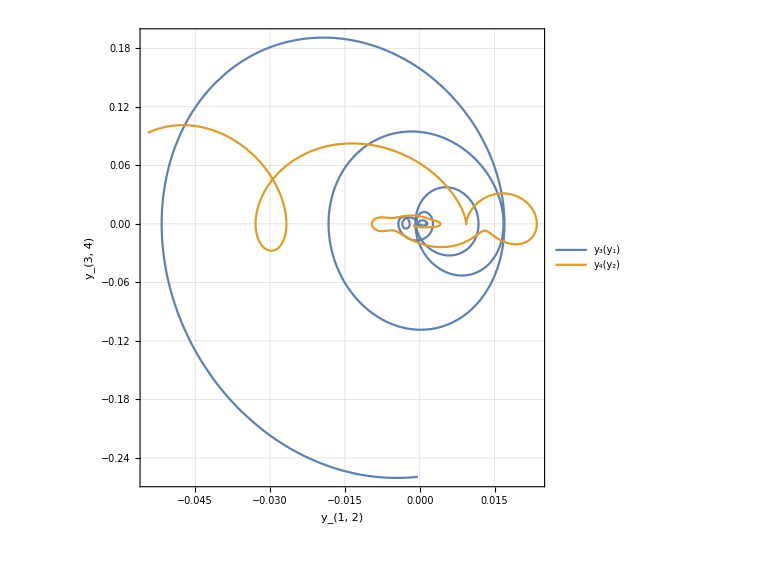

```mathematica
(*Ausgabe*)
plot=ParametricPlot[
Evaluate[{{𝓎[t][[1]],𝓎[t][[3]]},{𝓎[t][[2]],𝓎[t][[4]]}}],{t,𝓉ℬℯ𝓇ℯ𝒾𝒸𝒽[[1]],𝓉ℬℯ𝓇ℯ𝒾𝒸𝒽[[2]]},
PlotRange->All,Frame->True,FrameLabel->{"y_(1, 2)","y_(3, 4)"},GridLines->Automatic,
PlotLegends->{"y_3(y_1)","y_4(y_2)"},
AspectRatio->1,ImageSize->Large];
Print[Show[plot]]
```